```mathematica
dt = 0.0001;
tmax = 20;
Nn = Evaluate[tmax/dt]//Round;
```

```mathematica
tT = Table[i dt,{i,0,Nn}];
```

```mathematica
ξ1 = RandomVariate[NormalDistribution[0,√dt],Nn];
ξ2 = RandomVariate[NormalDistribution[0,√dt],Nn];
ξ3 = RandomVariate[NormalDistribution[0,√dt],Nn];
ξ4 = RandomVariate[NormalDistribution[0,√dt],Nn];
ξ5 = RandomVariate[NormalDistribution[0,√dt],Nn];
ξ6 = RandomVariate[NormalDistribution[0,√dt],Nn];
ξ7 = RandomVariate[NormalDistribution[0,√dt],Nn];
ξ8 = RandomVariate[NormalDistribution[0,√dt],Nn];
ξ9 = RandomVariate[NormalDistribution[0,√dt],Nn];
ξ10 = RandomVariate[NormalDistribution[0,√dt],Nn];
ξ11 = RandomVariate[NormalDistribution[0,√dt],Nn];
ξ12 = RandomVariate[NormalDistribution[0,√dt],Nn];
```

```mathematica
x = ConstantArray[1,Nn+1];
y = ConstantArray[1,Nn+1];
z = ConstantArray[1,Nn+1];
```

```mathematica
V= 1000;
```

### Steady State

```mathematica
VvalsSS = {V0->2,V1->2 , V4->5, kf->1,k->10,β-> 0.01,ϵ->0.1 ,VM2->6,k2->0.1,VM3->20,m->2,kx->0.5,ky->0.2,kz->0.2,VM5->30,k5->0.3,kd->0.5,p->2,n->4};
For[i=1,i<=Nn,i++,
x[[i+1]] =( x[[i]] + (V0+V1 β-k x[[i]]-(VM2 x[[i]]^2)/(k2^2+x[[i]]^2)+kf y[[i]]+(VM3 x[[i]]^m y[[i]]^2 z[[i]]^4)/((kx^m+x[[i]]^m) (ky^2+y[[i]]^2) (kz^4+z[[i]]^4)))*dt +1/(√V)(√V0 ξ1[[i]] + √(V1 β) ξ2[[i]]- √(VM2 x[[i]]^2/(k2^2 + x[[i]]^2))  ξ3[[i]]+ √(VM3 x[[i]]^m/(kx^m + x[[i]]^m)y[[i]]^2/(ky^2 + y[[i]]^2)z[[i]]^4/(kz^4 + z[[i]]^4))  ξ4[[i]]+ √(kf y[[i]])  ξ5[[i]]- √kx  ξ6[[i]])/.VvalsSS ); y[[i+1]] =( y[[i]] + ((VM2 x[[i]]^2)/(k2^2+x[[i]]^2)-kf y[[i]]-(VM3 x[[i]]^m y[[i]]^2 z[[i]]^4)/((kx^m+x[[i]]^m) (ky^2+y[[i]]^2) (kz^4+z[[i]]^4)))dt + 1/(√V)(√(VM2 x[[i]]^2/(k2^2 + x[[i]]^2)) ξ7[[i]]- √(VM3 x[[i]]^m/(kx^m + x[[i]]^m)) ξ8[[i]]- √(kf y[[i]])ξ9[[i]])/.VvalsSS );z[[i+1]] = (z[[i]]+ (V4 β-ϵ z[[i]]-(VM5 x[[i]]^n z[[i]]^p)/((kd^n+x[[i]]^n) (k5^p+z[[i]]^p)))dt + 1/(√V)(√(V4 β) ξ10[[i]]- √(VM5 z[[i]]^p/(k5^p + z[[i]]^p)x[[i]]^n/(kd^n + x[[i]]^n)) ξ11[[i]]- √(ϵ z[[i]])ξ12[[i]]) /.VvalsSS );]
```

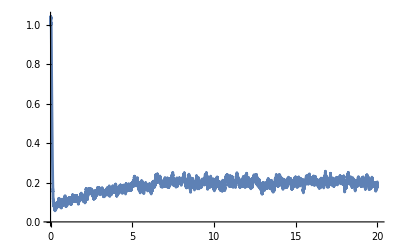

```mathematica
ListLinePlot[Transpose[{tT,x}],PlotRange->All]
```

### Simple Periodic Oscillations

```mathematica
VvalsSPO = {V0->2,V1->2 , V4->2, kf->1,k->10,β-> 0.5,ϵ->0.1 ,VM2->6,k2->0.1,VM3->20,m->2,kx->0.5,ky->0.2,kz->0.2,VM5->5,k5->1,kd->0.4,p->2,n->4};
For[i=1,i<=Nn,i++,
x[[i+1]] =( x[[i]] + (V0+V1 β-k x[[i]]-(VM2 x[[i]]^2)/(k2^2+x[[i]]^2)+kf y[[i]]+(VM3 x[[i]]^m y[[i]]^2 z[[i]]^4)/((kx^m+x[[i]]^m) (ky^2+y[[i]]^2) (kz^4+z[[i]]^4)))*dt +1/(√V)(√V0 ξ1[[i]] + √(V1 β) ξ2[[i]]- √(VM2 x[[i]]^2/(k2^2 + x[[i]]^2))  ξ3[[i]]+ √(VM3 x[[i]]^m/(kx^m + x[[i]]^m)y[[i]]^2/(ky^2 + y[[i]]^2)z[[i]]^4/(kz^4 + z[[i]]^4))  ξ4[[i]]+ √(kf y[[i]])  ξ5[[i]]- √kx  ξ6[[i]])/.VvalsSPO  ); y[[i+1]] =( y[[i]] + ((VM2 x[[i]]^2)/(k2^2+x[[i]]^2)-kf y[[i]]-(VM3 x[[i]]^m y[[i]]^2 z[[i]]^4)/((kx^m+x[[i]]^m) (ky^2+y[[i]]^2) (kz^4+z[[i]]^4)))dt + 1/(√V)(√(VM2 x[[i]]^2/(k2^2 + x[[i]]^2)) ξ7[[i]]- √(VM3 x[[i]]^m/(kx^m + x[[i]]^m)) ξ8[[i]]- √(kf y[[i]])ξ9[[i]])/.VvalsSPO  );z[[i+1]] = (z[[i]]+ (V4 β-ϵ z[[i]]-(VM5 x[[i]]^n z[[i]]^p)/((kd^n+x[[i]]^n) (k5^p+z[[i]]^p)))dt + 1/(√V)(√(V4 β) ξ10[[i]]- √(VM5 z[[i]]^p/(k5^p + z[[i]]^p)x[[i]]^n/(kd^n + x[[i]]^n)) ξ11[[i]]- √(ϵ z[[i]])ξ12[[i]]) /.VvalsSPO  );]
```

```mathematica
ListLinePlot[Transpose[{tT,x}],PlotRange->All]
```

-Graphics-

### Bursting

```mathematica
VvalsB = {V0->2,V1->2 , V4->2.5, kf->1,k->10,β-> 0.46,ϵ->0.1 ,VM2->6,k2->0.1,VM3->20,m->4,kx->0.3,ky->0.2,kz->0.1,VM5->30,k5->1,kd->0.6,p->1,n->2};
For[i=1,i<=Nn,i++,
x[[i+1]] =( x[[i]] + (V0+V1 β-k x[[i]]-(VM2 x[[i]]^2)/(k2^2+x[[i]]^2)+kf y[[i]]+(VM3 x[[i]]^m y[[i]]^2 z[[i]]^4)/((kx^m+x[[i]]^m) (ky^2+y[[i]]^2) (kz^4+z[[i]]^4)))*dt +1/(√V)(√V0 ξ1[[i]] + √(V1 β) ξ2[[i]]- √(VM2 x[[i]]^2/(k2^2 + x[[i]]^2))  ξ3[[i]]+ √(VM3 x[[i]]^m/(kx^m + x[[i]]^m)y[[i]]^2/(ky^2 + y[[i]]^2)z[[i]]^4/(kz^4 + z[[i]]^4))  ξ4[[i]]+ √(kf y[[i]])  ξ5[[i]]- √kx  ξ6[[i]])/.VvalsB ); y[[i+1]] =( y[[i]] + ((VM2 x[[i]]^2)/(k2^2+x[[i]]^2)-kf y[[i]]-(VM3 x[[i]]^m y[[i]]^2 z[[i]]^4)/((kx^m+x[[i]]^m) (ky^2+y[[i]]^2) (kz^4+z[[i]]^4)))dt + 1/(√V)(√(VM2 x[[i]]^2/(k2^2 + x[[i]]^2)) ξ7[[i]]- √(VM3 x[[i]]^m/(kx^m + x[[i]]^m)) ξ8[[i]]- √(kf y[[i]])ξ9[[i]])/.VvalsB  );z[[i+1]] = (z[[i]]+ (V4 β-ϵ z[[i]]-(VM5 x[[i]]^n z[[i]]^p)/((kd^n+x[[i]]^n) (k5^p+z[[i]]^p)))dt + 1/(√V)(√(V4 β) ξ10[[i]]- √(VM5 z[[i]]^p/(k5^p + z[[i]]^p)x[[i]]^n/(kd^n + x[[i]]^n)) ξ11[[i]]- √(ϵ z[[i]])ξ12[[i]]) /.VvalsB  );]
```

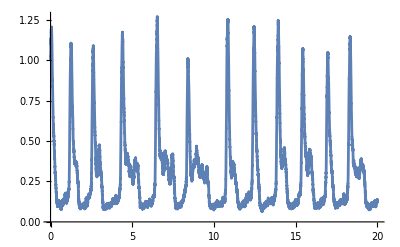

```mathematica
ListLinePlot[Transpose[{tT,x}],PlotRange->All]
```

### Chaos

```mathematica
VvalsC= {V0->2,V1->2 , V4->3, kf->1,k->10,β-> 0.65,ϵ->13 ,VM2->6,k2->0.1,VM3->30,m->2,kx->0.6,ky->0.3,kz->0.1,VM5->50,k5->0.3194,kd->1,p->1,n->4};
For[i=1,i<=Nn,i++,
x[[i+1]] =( x[[i]] + (V0+V1 β-k x[[i]]-(VM2 x[[i]]^2)/(k2^2+x[[i]]^2)+kf y[[i]]+(VM3 x[[i]]^m y[[i]]^2 z[[i]]^4)/((kx^m+x[[i]]^m) (ky^2+y[[i]]^2) (kz^4+z[[i]]^4)))*dt +1/(√V)(√V0 ξ1[[i]] + √(V1 β) ξ2[[i]]- √(VM2 x[[i]]^2/(k2^2 + x[[i]]^2))  ξ3[[i]]+ √(VM3 x[[i]]^m/(kx^m + x[[i]]^m)y[[i]]^2/(ky^2 + y[[i]]^2)z[[i]]^4/(kz^4 + z[[i]]^4))  ξ4[[i]]+ √(kf y[[i]])  ξ5[[i]]- √kx  ξ6[[i]])/.VvalsC); y[[i+1]] =( y[[i]] + ((VM2 x[[i]]^2)/(k2^2+x[[i]]^2)-kf y[[i]]-(VM3 x[[i]]^m y[[i]]^2 z[[i]]^4)/((kx^m+x[[i]]^m) (ky^2+y[[i]]^2) (kz^4+z[[i]]^4)))dt + 1/(√V)(√(VM2 x[[i]]^2/(k2^2 + x[[i]]^2)) ξ7[[i]]- √(VM3 x[[i]]^m/(kx^m + x[[i]]^m)) ξ8[[i]]- √(kf y[[i]])ξ9[[i]])/.VvalsC );z[[i+1]] = (z[[i]]+ (V4 β-ϵ z[[i]]-(VM5 x[[i]]^n z[[i]]^p)/((kd^n+x[[i]]^n) (k5^p+z[[i]]^p)))dt + 1/(√V)(√(V4 β) ξ10[[i]]- √(VM5 z[[i]]^p/(k5^p + z[[i]]^p)x[[i]]^n/(kd^n + x[[i]]^n)) ξ11[[i]]- √(ϵ z[[i]])ξ12[[i]]) /.VvalsC );]
```

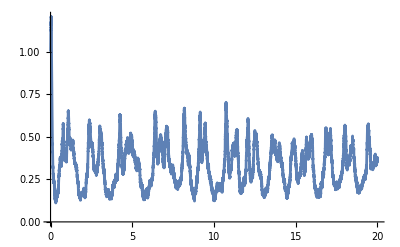

```mathematica
ListLinePlot[Transpose[{tT,x}],PlotRange->All]
```

### Period Doubling Sequences

```mathematica
VvalsPDS= {V0->2,V1->2 , V4->3, kf->1,k->10,β-> 0.7,ϵ->13 ,VM2->6,k2->0.1,VM3->30,m->2,kx->0.6,ky->0.3,kz->0.1,VM5->50,k5->0.3194,kd->1,p->1,n->4};
For[i=1,i<=Nn,i++,
x[[i+1]] =( x[[i]] + (V0+V1 β-k x[[i]]-(VM2 x[[i]]^2)/(k2^2+x[[i]]^2)+kf y[[i]]+(VM3 x[[i]]^m y[[i]]^2 z[[i]]^4)/((kx^m+x[[i]]^m) (ky^2+y[[i]]^2) (kz^4+z[[i]]^4)))*dt +1/(√V)(√V0 ξ1[[i]] + √(V1 β) ξ2[[i]]- √(VM2 x[[i]]^2/(k2^2 + x[[i]]^2))  ξ3[[i]]+ √(VM3 x[[i]]^m/(kx^m + x[[i]]^m)y[[i]]^2/(ky^2 + y[[i]]^2)z[[i]]^4/(kz^4 + z[[i]]^4))  ξ4[[i]]+ √(kf y[[i]])  ξ5[[i]]- √kx  ξ6[[i]])/.VvalsPDS); y[[i+1]] =( y[[i]] + ((VM2 x[[i]]^2)/(k2^2+x[[i]]^2)-kf y[[i]]-(VM3 x[[i]]^m y[[i]]^2 z[[i]]^4)/((kx^m+x[[i]]^m) (ky^2+y[[i]]^2) (kz^4+z[[i]]^4)))dt + 1/(√V)(√(VM2 x[[i]]^2/(k2^2 + x[[i]]^2)) ξ7[[i]]- √(VM3 x[[i]]^m/(kx^m + x[[i]]^m)) ξ8[[i]]- √(kf y[[i]])ξ9[[i]])/.VvalsPDS );z[[i+1]] = (z[[i]]+ (V4 β-ϵ z[[i]]-(VM5 x[[i]]^n z[[i]]^p)/((kd^n+x[[i]]^n) (k5^p+z[[i]]^p)))dt + 1/(√V)(√(V4 β) ξ10[[i]]- √(VM5 z[[i]]^p/(k5^p + z[[i]]^p)x[[i]]^n/(kd^n + x[[i]]^n)) ξ11[[i]]- √(ϵ z[[i]])ξ12[[i]]) /.VvalsPDS );]
```

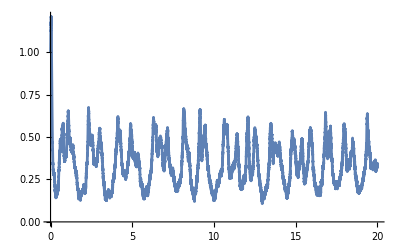

```mathematica
ListLinePlot[Transpose[{tT,x}],PlotRange->All]
```